# Юрьев В. А. ПО-4 Лабораторная работа №4

```mathematica
(* PlotRangePadding- это опция для графических функций, задающая отступ внутреннего изображения от границ внешнего графика,  указанного в PlotRange. 
PlotRegion опция для графических функций, которая определяет, какую область конечной области отображения должен заполнять график.
Метод ContourShading определяет набор цветов для отображения границ контурного графика.\*)
Упражнение 11.2а (Что следует вставить вместо Yааaа чтобы получить график снизу)
```

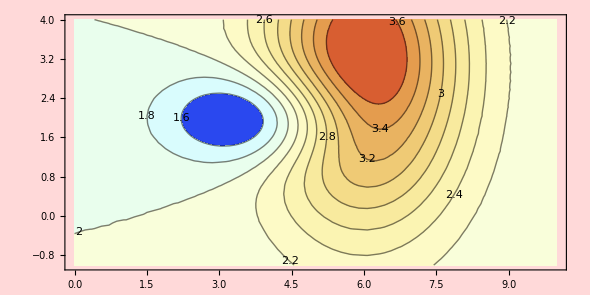

```mathematica
xmin:=0;xmax:=10;
ymin:=-1;ymax:=4;
aspRat =(ymax-ymin)/(xmax-xmin);

fXY[x_,y_] := 2-E^(-(x/2-2)^2-(y-2)^2)+2*E^(-(x/2-3)^2-(y/3-1)^2);
grf2Da=ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->11,ContourLabels->All,ColorFunction->"LightTemperatureMap",BaseStyle->14,AspectRatio->aspRat,ImageSize->590,PlotRangePadding->{{1,4}, {0,2}},Background->LightRed]
```

```mathematica
Упражнение 11.2b (Что следует вставить вместо Ybbbb чтобы получить график снизу)
(* PlotRegion опция для графических функций, которая определяет, какую область конечной области отображения должен заполнять график.
```

```mathematica
ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->11,ContourLabels->All,ColorFunction->"LightTemperatureMap",BaseStyle->14,AspectRatio->aspRat,ImageSize->590,PlotRegion->{{0.3,1},{0,0.8}},Background->LightRed]
```

-Graphics-

```mathematica
Упражнение 11.2c (Что следует вставить вместо Ycccc чтобы получить график снизу)
(*Метод ContourShading определяет набор цветов для отображения границ контурного графика.\*)
```

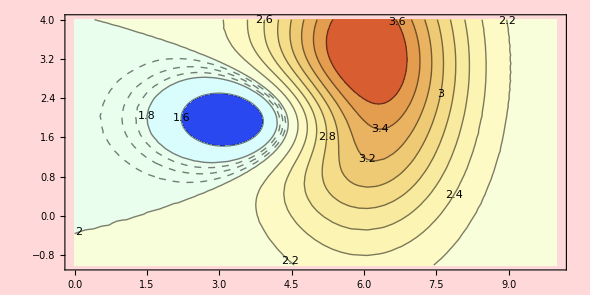

```mathematica
Show[
ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->11,ContourLabels->All,ColorFunction->"LightTemperatureMap",BaseStyle->14, AspectRatio->aspRat,ImageSize->590,Background->LightRed],

ContourPlot[fXY[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->{1.85,1.9,1.95},ContourStyle->Dashed,ContourShading->{None},AspectRatio->aspRat,ImageSize->590]
]
```

```mathematica
Упражнение 11.1d(Что следует вставить вместо Ydddd чтобы получить график снизу)
```

```mathematica
(* Inset[obj,pos,opos,size] 
Метод Inset позволяет вставить почти любой объект с заданием его размеров и местоположения на графике
```

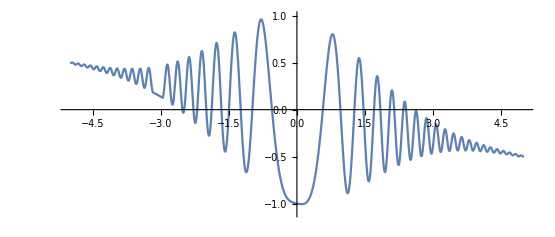

```mathematica
f3[x_] :=(-E^(-0.2*x^2))*Cos[5*x^2]-0.1*x
grf1DdFrgm=Plot[f3[x],{x,-4,-3},AspectRatio->3/7];
Plot[f3[x],{x,-5,5},AspectRatio->3/7,Epilog->Inset[grf1DdFrgm,Scaled[{0.05, .05}],Scaled[{0, 0}],4],PlotRange->{-1.1,1},PlotRangeClipping->False,ImageSize->550]
```

```mathematica
Упражнение 11.1e (Что следует вставить вместо Yeeee чтобы получить график снизу)
```

```mathematica
(* Hue представляет цвет в цветовом пространстве HSB с оттенком [x].
```

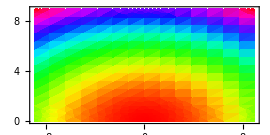
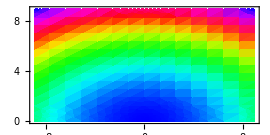

```mathematica
grf2Dd=DensityPlot[x^2+3*y^2,{x,-9,9},{y,0,9},BaseStyle->16,AspectRatio->1/2,PlotLegends->Placed[Automatic,Above],ColorFunction->Hue,ImageSize->270];

grf2De=DensityPlot[x^2+3*y^2,{x,-9,9},{y,0,9},BaseStyle->16,AspectRatio->1/2,PlotLegends->Placed[Automatic,Above],ColorFunction-> (Hue[60/90-#]&),ImageSize->270];

Row[{grf2Dd,grf2De},Spacer[5]]
```